# Double GGX NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## definitions and derivations

The NDF that is to GGX as GGX is to Beckmann is:

```mathematica
DoubleGGX`D[u_,α_]:=(α^2 (1-u^2+ⅇ^(-(u^2 α^2)/(-1+u^2)) (1+u^2 (-1+α^2)) ExpIntegralEi[(u^2 α^2)/(-1+u^2)]))/(π (-1+u^2)^3)HeavisideTheta[u]
```

```mathematica
DoubleGGX`σ[u_,α_]:=1/2 (u+√π Abs[u] HypergeometricU[-1/2,0,(-1+1/u^2) α^2])
```

```mathematica
DoubleGGX`Λ[u_,α_]:=1/2 (-1+(√π Abs[u] HypergeometricU[-1/2,0,(-1+1/u^2) α^2])/u)
```

```mathematica
(1+DoubleGGX`Λ[u,α])u==DoubleGGX`σ[u,α]//FullSimplify
```

True

```mathematica
FullSimplify[(DoubleGGX`Λ[u,α])u==DoubleGGX`σ[-u,α],Assumptions->0<α<1&&-1<u<1]
```

True

```mathematica
FunctionExpand[HypergeometricU[-1/2,0,(-1+1/u^2) α^2]]
```

-(ⅇ^(1/2 (-1+1/u^2) α^2) (-1+u^2) α^2 BesselK[0,1/2 (-1+1/u^2) α^2])/(2 √π u^2)-(ⅇ^(1/2 (-1+1/u^2) α^2) (-1+u^2) α^2 BesselK[1,1/2 (-1+1/u^2) α^2])/(2 √π u^2)

```mathematica
FullSimplify[DoubleGGX`Λ[u,u/(√(1-u^2) x)],Assumptions->0<u<1&&x>0]
```

1/2 (-1+√π HypergeometricU[-1/2,0,1/x^2])

### shape invariant f(x)

```mathematica
FullSimplify[DoubleGGX`D[u,α] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0]
```

-(x^2+ⅇ^(1/x^2) (1+x^2) ExpIntegralEi[-1/x^2])/(π x^6)

### derivation

```mathematica
Integrate[Exp[-αB]GGX`D[u,α/√αB],{αB,0,Infinity},Assumptions->0<u<1&&0<α<1]
```

$Aborted

```mathematica
Integrate[Exp[-αB]GGX`σ[u,α/√αB],{αB,0,Infinity},Assumptions->-1<u<1&&0<α<1]
```

1/2 (u+√π Abs[u] HypergeometricU[-1/2,0,(-1+1/u^2) α^2])

```mathematica
Integrate[Exp[-αB]GGX`Λ[u,α/√αB],{αB,0,Infinity},Assumptions->-1<u<1&&0<α<1]
```

1/2 (-1+(√π Abs[u] HypergeometricU[-1/2,0,(-1+1/u^2) α^2])/u)

### distribution of slopes

```mathematica
FullSimplify[DoubleGGX`D[1/(√(p^2+q^2+1)),α](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

-(α^2 (p^2+q^2+ⅇ^(α^2/(p^2+q^2)) (p^2+q^2+α^2) ExpIntegralEi[-α^2/(p^2+q^2)]))/(π (p^2+q^2)^3)

```mathematica
DoubleGGX`P22[p_,q_,α_]:=-(α^2 (p^2+q^2+ⅇ^(α^2/(p^2+q^2)) (p^2+q^2+α^2) ExpIntegralEi[-α^2/(p^2+q^2)]))/(π (p^2+q^2)^3)
```

```mathematica
Integrate[DoubleGGX`P22[p,q,α],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1]
```

1

```mathematica
Integrate[DoubleGGX`P22[p,q,1],{q,-Infinity,Infinity},Assumptions->α>0&&Im[p]==0]
```

$Aborted

### compare σ to delta integral:

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

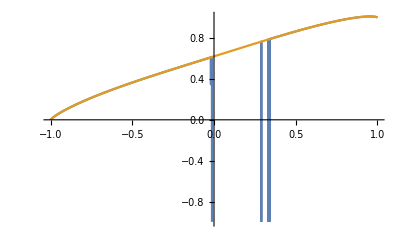

```mathematica
With[{α=.7},
Plot[{
 Quiet[NIntegrate[DoubleGGX`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
DoubleGGX`σ[u,α]
},{u,-1,1}]
]
```

### importance sampling

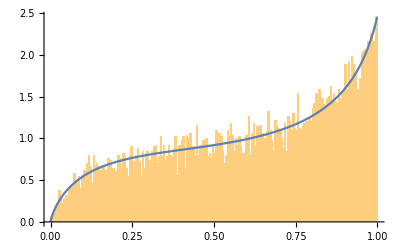

```mathematica
With[{α=.9},
Show[
Histogram[Table[√(1/(1-(α/√#)^2+(α/√#)^2/RandomReal[]))&[-Log[RandomReal[]]],{i,Range[10000]}],200,"PDF"],
Plot[DoubleGGX`D[u,α]2 Pi u,{u,0,.999},PlotRange->All]
]
]
```